```mathematica
目标函数 ，二进制
```

```mathematica
f[x_]:=Total[x]
```

```mathematica
IntegerDigits[7,2]
```

{1,1,1}

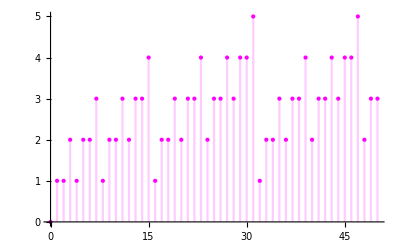

```mathematica
DiscretePlot[Total@IntegerDigits[x,2],{x,0,50},PlotStyle->{Magenta,PointSize[Large]}]
```

```mathematica
Plot3D[Total[#]+Times@@#&[{x,y}],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

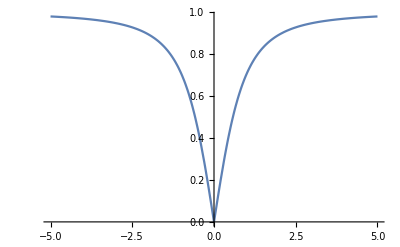

```mathematica
Plot[Abs[x/(√(x^2+1))],{x,-5,5}]
```

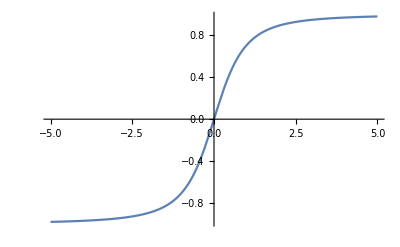

```mathematica
Plot[x/(√(x^2+1)),{x,-5,5}]
```

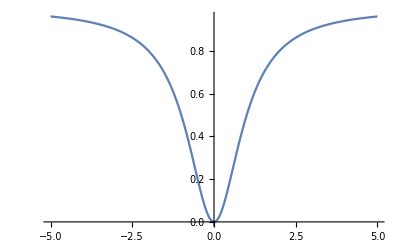

```mathematica
Plot[Abs[x^2/(x^2+1)],{x,-5,5}]
```